# Molecular Exact Diagonalization

## Read in the Hamiltonian Parameters

```mathematica
ReadFile=OpenRead["/home/thomas/Libraries/NEdyson/h2H.dat"];
nao=Read[ReadFile,Number];
mu=Table[Read[ReadFile,Number],{i,1,2}];
h0=Table[Table[Read[ReadFile,Number],{j,1,nao}],{i,1,nao}];
Uijkl=Table[Table[Table[Table[Read[ReadFile,Number],{l,1,nao}],{k,1,nao}],{j,1,nao}],{i,1,nao}];
naso =2 nao;
states=2^naso;
```

```mathematica
c=Array[0,{2,nao,states,states}];
cdag=Array[0,{2,nao,states,states}];
Table[Table[c[[j,i,;;,;;]]=ArrayReshape[ReadList["~/Libraries/NEdyson/ED/hybfermion/build/c_"<>ToString[(j-1)*nao+i-1]<>".dat",Number],{states,states}],{i,1,nao}],{j,1,2}];
Table[Table[cdag[[j,i,;;,;;]]=ArrayReshape[ReadList["~/Libraries/NEdyson/ED/hybfermion/build/cdag_"<>ToString[(j-1)*nao+i-1]<>".dat",Number],{states,states}],{i,1,nao}],{j,1,2}];
IM=IdentityMatrix[states];
```

## Define the Hamiltonian

```mathematica
datadir="~/Libraries/NEdyson/";
H=Sum[Sum[Sum[h0[[i,j]] cdag[[s]][[i]].c[[s]][[j]],{j,1,nao}],{i,1,nao}],{s,1,2}]-Sum[Sum[mu[[s]] cdag[[s]][[j]].c[[s]][[j]],{j,1,nao}],{s,1,2}]+0.5 Sum[Sum[Sum[Sum[Sum[Sum[Uijkl[[i,j,k,l]] cdag[[s]][[i]].cdag[[sp]][[k]].c[[sp]][[l]].c[[s]][[j]],{l,1,nao}],{k,1,nao}],{j,1,nao}],{i,1,nao}],{s,1,2}],{sp,1,2}];
```

```mathematica
β=50;
Z=N[Tr[MatrixExp[-β H]]];
HEigVals =Eigensystem[H][[1]];
HEigVecs = Map[Normalize,Eigensystem[H][[2]]];
Print["Check if the Hamiltonian is Diagonalizable: "<>ToString[DiagonalizableMatrixQ[H]]<>" Max err: "]
Max[N[H-Transpose[HEigVecs].DiagonalMatrix[HEigVals].HEigVecs]]
cdagTrans=Table[Table[HEigVecs.cdag[[s]][[i]].Transpose[HEigVecs],{i,1,nao}],{s,1,2}];
cTrans=Table[Table[HEigVecs.c[[s]][[i]].Transpose[HEigVecs],{i,1,nao}],{s,1,2}];
```

Check if the Hamiltonian is Diagonalizable: True Max err:

8.88178×10^-16

## Make Matsubara Functions

```mathematica
ReadFile=OpenRead[datadir<>"/_GM.dat"];
Params=Table[Read[ReadFile,Number],{i,1,6}];
GMNEdyson=Table[Table[Read[ReadFile,Number],{i,1,2*Params[[3]]^2}],{t,1,Params[[2]]+1}];
GM=-Table[Table[Table[Table[1/Z Tr[DiagonalMatrix[Exp[(-β+τ)HEigVals]].cTrans[[s]][[i]].DiagonalMatrix[Exp[-τ HEigVals]].cdagTrans[[s]][[j]]],{τ,0,β,β/100}],{i,1,nao}],{j,1,nao}],{s,1,2}];
(*GM=-Table[Table[Table[1/Z Tr[MatrixExp[(-β+τ)H].c[[i]].MatrixExp[-τ H].cdag[[j]]],{τ,0,β,β/100}],{i,1,sites2,2}],{j,1,sites2,2}];*)
```

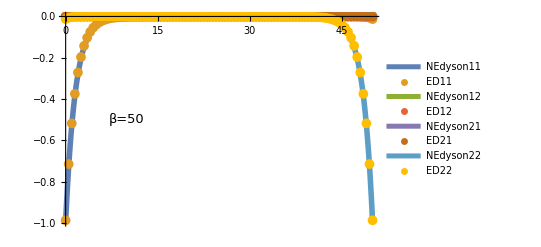

```mathematica
MPlot=ListPlot[Flatten[Table[Table[{Transpose[{Range[0,β+0.000001,β/1000],GMNEdyson[[;;,2 nao (i-1)+2j-1]]}],Transpose[{Range[0,β,β/100],GM[[1,i,j,;;]]}]},{i,1,nao}],{j,1,nao}],2],
PlotRange->Full,
Joined->Flatten[Table[{True, False},{i,1,nao*nao}]],
PlotStyle->{Thickness[0.01]},
PlotMarkers->Flatten[Table[{None,Style[•,10]},{i,1,nao,nao}]],PlotLegends->Flatten[Table[{"NEdyson"<>ToString[Quotient[i+1,nao]]<>ToString[Mod[i-1,nao]+1],"ED"<>ToString[Quotient[i+1,nao]]<>ToString[Mod[i-1,nao]+1]},{i,1,nao*nao}]],Epilog->{Text[Style["β="<>ToString[β],13],{10,-0.5}]}]
```

```mathematica
Export["H2Mat.eps",MPlot]
```

H2Mat.eps

## Retarded

```mathematica
ReadFile=OpenRead[datadir<>"/_GR.dat"];
Params=Table[Read[ReadFile,Number],{i,1,6}];
GRNEdyson =Table[Table[0,{j,1,2 Params[[3]]^2}],{i,1,Params[[1]]+1}];
Table[Table[GRNEdyson[[t,i]]=Read[ReadFile,Number],{i,1,2 Params[[3]]^2}];Table[Read[ReadFile,Number],{tp,1,2 Params[[3]]^2*(t-1)}];,{t,1,Params[[1]]+1}];
```

```mathematica
GLf1D[s_,t_,i_,j_]:=I/Z Tr[DiagonalMatrix[Exp[-(β+I t)HEigVals]].cdagTrans[[s]][[j]].DiagonalMatrix[Exp[(I t)HEigVals]].cTrans[[s]][[i]]];
GGf1D[s_,t_,i_,j_]:=-I/Z Tr[DiagonalMatrix[Exp[-(β-I t)HEigVals]].cTrans[[s]][[i]].DiagonalMatrix[Exp[(-I t )HEigVals]].cdagTrans[[s]][[j]]];
GRf1D[s_,t_,i_,j_]:= GGf1D[s,t,i,j]-GLf1D[s,t,i,j];
```

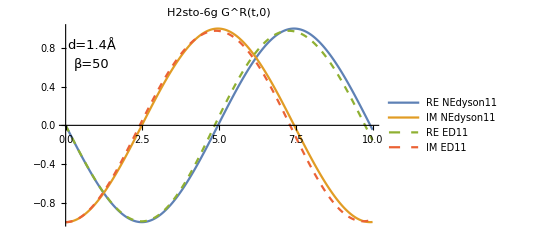
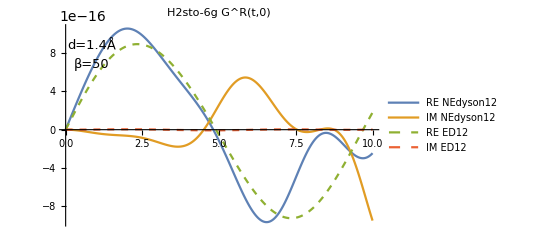
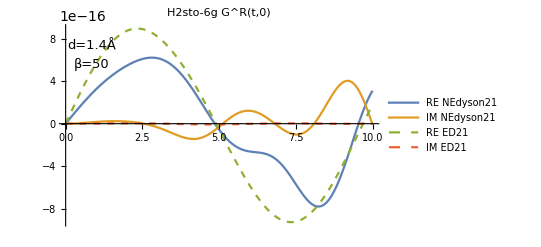
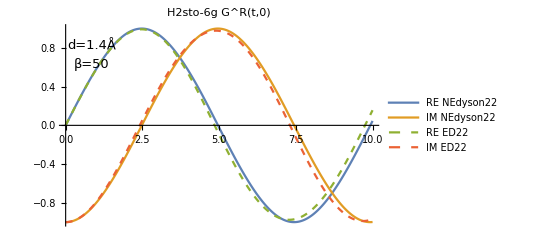

```mathematica
GRPlots=ListPlot[
{Transpose[{Range[0,Params[[1]]*Params[[4]]+10^-10,Params[[4]]],
GRNEdyson[[;;,2*nao*(#[[1]]-1)+2*(#[[2]]-1)+1]]}],
Transpose[{Range[0,Params[[1]]*Params[[4]]+10^-10,Params[[4]]],
GRNEdyson[[;;,2*nao*(#[[1]]-1)+2*(#[[2]]-1)+2]]}],Transpose[{Range[0,Params[[1]]*Params[[4]],Params[[1]]*Params[[4]]/500],
Re[Function[{t},GRf1D[1,t,#[[1]],#[[2]]]]/@Range[0,Params[[1]]*Params[[4]],Params[[1]]*Params[[4]]/500]]}],Transpose[{Range[0,Params[[1]]*Params[[4]],Params[[1]]*Params[[4]]/500],
Im[Function[{t},GRf1D[1,t,#[[1]],#[[2]]]]/@Range[0,Params[[1]]*Params[[4]],Params[[1]]*Params[[4]]/500]]}]},
PlotStyle->{Solid,Solid,Dashed,Dashed},
PlotMarkers->Flatten[Table[{None,None,None,None},{i,1,nao,nao}]],
Joined->{True,True,True,True},
PlotLegends->{"RE NEdyson"<>ToString[#[[1]]]<>ToString[#[[2]]],"IM NEdyson"<>ToString[#[[1]]]<>ToString[#[[2]]],"RE ED"<>ToString[#[[1]]]<>ToString[#[[2]]],"IM ED"<>ToString[#[[1]]]<>ToString[#[[2]]]},
Epilog->{Text[Style["d=1.4Å",13],Scaled[{0.1,0.9}]],Text[Style["β="<>ToString[β],13],Scaled[{0.1,0.8}]]},
PlotLabel->"H2sto-6g G^R(t,0)"]&/@Flatten[Table[Table[{i,j},{j,1,nao}],{i,1,nao}],1]
```

```mathematica
Table[Table[Export["DecompH2Ret"<>ToString[i]<>ToString[j]<>".eps",GRPlots[[(i-1)*nao+j]]],{j,1,nao}],{i,1,nao}]
```

{{DecompH2Ret11.eps,DecompH2Ret12.eps},{DecompH2Ret21.eps,DecompH2Ret22.eps}}

## Spectral Function

```mathematica
ReadFile=OpenRead[datadir<>"/_A.dat"];
Param=Table[Read[ReadFile,Number],{i,1,6}];
ANEdysondata=Table[Table[0,{i,Param[[3]]^2}],{w,1,Param[[2]]}];
Table[Read[ReadFile,Number];,{i,1,Param[[3]]^2 (Quotient[Param[[1]],2]-1)Param[[2]]}];
Table[Table[ANEdysondata[[w,i]]=Read[ReadFile,Number];,{i,1,Param[[3]]^2}],{w,1,Param[[2]]}];
```

```mathematica
GRf1Dchop[s_,trel_,i_,j_]:=Chop[Simplify[GRf1D[s,trel,i,j]],0.001];
FTf1Dchop[s_,tmax_,w_,i_,j_]:=-1/Pi Im[Integrate[GRf1Dchop[s,trel,i,j]Exp[I w trel],{trel,0,tmax}]];
FTf1D[s_,tmax_,w_,i_,j_]:=-1/Pi Im[Integrate[GRf1D[s,trel,i,j]Exp[I w trel],{trel,0,tmax}]];
Lorentz[x_,a_,γ_]:=1/(Pi γ)(γ^2/((x-a)^2+γ^2));
LehmannA[s_,w_,i_,j_,γ_]:=1/Z Sum[Sum[(HEigVecs[[m]].cdag[[s]][[i]].HEigVecs[[n]])*(HEigVecs[[m]].cdag[[s]][[j]].HEigVecs[[n]])(Exp[-β HEigVals[[m]]]+Exp[-β HEigVals[[n]]])Lorentz[w,HEigVals[[m]]-HEigVals[[n]],γ],{n,1,states}],{m,1,states}]
```

```mathematica
wlist=Table[w,{w,-2,2,0.01}];
wftlist=Table[w,{w,-2,2,0.1}];
FTdata=Table[Table[Function[{w},FTf1Dchop[1,10,w,i,j]]/@wftlist,{j,1,nao}],{i,1,nao}];
Lehmanndata=Table[Table[Function[{w},LehmannA[1,w,i,j,0.06]]/@wlist,{j,1,nao}],{i,1,nao}];
```

```mathematica
Length[ANEdysondata[[1]]]
```

4

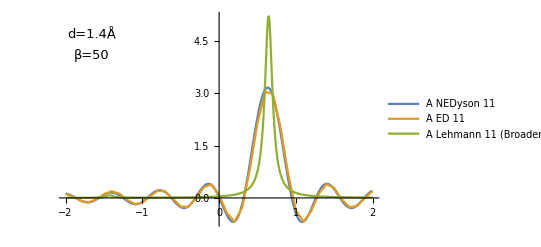
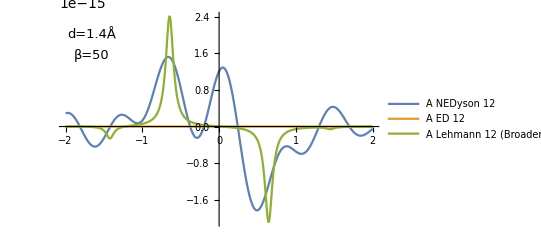
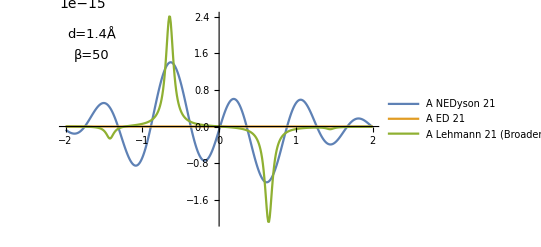
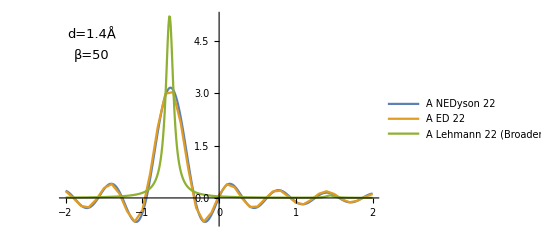

```mathematica
Aplots=ListPlot[
{Transpose[{Range[-Param[[4]],Param[[4]]+10^-10,Param[[5]]],ANEdysondata[[;;,(#[[1]]-1)*nao+#[[2]]]]}],Transpose[{wftlist,FTdata[[#[[1]],#[[2]],;;]]}],Transpose[{wlist,Lehmanndata[[#[[1]],#[[2]],;;]]}]},Joined->True,PlotRange->Full,Epilog->{Text[Style["d=1.4Å",13],Scaled[{0.1,0.9}]],Text[Style["β="<>ToString[β],13],Scaled[{0.1,0.8}]]},PlotLegends->{"A NEDyson "<>ToString[#[[1]]]<>ToString[#[[2]]],"A ED "<>ToString[#[[1]]]<>ToString[#[[2]]],"A Lehmann "<>ToString[#[[1]]]<>ToString[#[[2]]]"\n(Broadened)"}]&/@Flatten[Table[Table[{i,j},{j,1,nao}],{i,1,nao}],1]
```

```mathematica
Table[Table[Export["DecompA"<>ToString[i]<>ToString[j]<>".eps",Aplots[[(i-1)*nao+j]]],{j,1,nao}],{i,1,nao}]
```

{{DecompA11.eps,DecompA12.eps},{DecompA21.eps,DecompA22.eps}}

## Junk Below here

```mathematica
wlist={1};
Timing[Table[Table[Function[{w},FTf1D[24,w,i,j]]/@wlist,{j,1,2sites,2}],{i,1,2sites,2}]]
```

{1}

{19.455,{{{-0.0560902},{0.0108044}},{{0.0108044},{-0.0838365}}}}

```mathematica
Timing[FTf1D[24,1,1,1]]
```

{4.62574,-0.0560902}

```mathematica
FTf1D[tmax_,w_,i_,j_]:=-1/Pi Im[Integrate[GRf1D[trel,i,j]Exp[I w trel],{trel,0,tmax}]];
```